```mathematica
Z=1;
a0 = 5.29177210544×10^-11;   (*Bohr radius *)
c=299792458; (* Speed of light *)
Ry =2.1798723611030*10^−18; (* Rydberg energy *) 
hbar=1.054571817*10^−34;
```

```mathematica
g0[n_] :=Sqrt[1/(2*(2n-1)!)] * 4*(4n)^n * Exp[-2n]*a0/Sqrt[Ry]
```

```mathematica
gup[1][n_, κ_] := Module[{product, Γterm},  (* to be used only for 1s to kp or 2p to kd*)
    product = Product[(1 + s^2 κ^2), {s, 1, n}];
    Γterm = 0;
    If[κ==0,1,Sqrt[product/(1 - Exp[-2π/κ])] * Exp[2n - 2/κ ArcTan[n κ]] * (1 + n^2 κ^2)^(-n-2)] * g0[n]
]
gup[2][n_, κ_] := (1/2) * Sqrt[(2n-1)*(1 + n^2 κ^2)] * gup[1][n, κ]
```

```mathematica
gup[i_][n_,  κ_] /;i>2 := Module[{l,term1, term2, term3},
  l=n-i+2;
    term1 = (4n^2 - 4l^2 + l(2l-1)(1 + n^2 κ^2)) * gup[i-1][n, κ];
    term2 = 2n * Sqrt[(n^2 - l^2)*(1 + (l+1)^2 κ^2)] * gup[i-2][n, κ];
    coeff = 2n*Sqrt[(n^2 - (l-1)^2)*(1 + l^2 κ^2)]; 
    (* Full solution *)
    (term1 - term2)/coeff
]
```

```mathematica
gdown[1][n_, κ_] := Module[{product, Γterm},
    1/(2n)Sqrt[(1+n^2κ^2)/(1 + (n-1)^2κ^2)] * gup[1][n,κ]
]
gdown[2][n_, κ_] := ((4+(n-1)(1+n^2κ^2))/(2n)) * Sqrt[(2n-1)/(1 + (n-2)^2 κ^2)] * gdown[1][n, κ]
```

```mathematica
gdown[i_][n_,  κ_] /;i>2 := Module[{l,term1, term2, term3},
  l=n-i+1;
    term1 = (4n^2 - 4l^2 + l(2l+1)(1 + n^2 κ^2)) * gdown[i-1][n, κ];
    term2 = 2n * Sqrt[(n^2 - (l+1)^2)*(1 + (l)^2 κ^2)] * gdown[i-2][n, κ];
    coeff = 2n*Sqrt[(n^2 - l^2)*(1 + (l-1)^2 κ^2)]; 
    (* Full solution *)
    (term1 - term2)/coeff
]
```

```mathematica
Sigma[n_, l_, W_,lprime_] := Module[{gValue, lmax,w},
    lmax = Max[l, lprime];
    w=(W+Ry/n^2)/hbar;
    gValue = gup[n-l][n, Sqrt[W/Ry]]; 
    (* Full formula *)
   (4*π^2*w*a0*2*Ry)/(3*c) * (n^4/Z^4)*10^4 (lmax/(2*l + 1))* Abs[gValue]^2
]
```

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

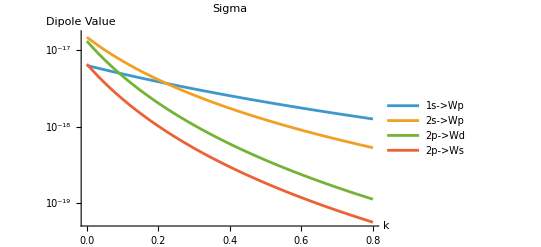

```mathematica
LogPlot[Evaluate[{Sigma[1,0,W* Ry,1],Sigma[2,0,W *Ry,1],Sigma[2,1,W* Ry,2],Sigma[2,1,W *Ry,0]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","2p->Wd","2p->Ws"},
 PlotRange ->{Automatic, {0,16*10^-18}}]
```

General::munfl: Exp[-9829.83] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

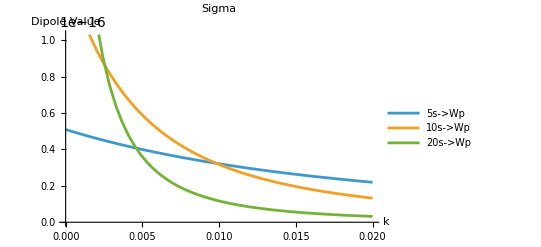

```mathematica
Plot[Evaluate[{Sigma[5,0,W Ry,1],Sigma[10,0,W Ry,1],Sigma[20,0,W Ry,1]}], {W, 0, 0.02},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"5s->Wp","10s->Wp","20s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
eE0=Sqrt[hbar];
Ei[i_]:=-Ry/i^2;
ωi[i_]:=Ei[i]/hbar;
(*T[w_]:=100;*)
SumPWOmega2up[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[((l+1)^2-m^2)/(4(l+1)^2-1),{m,-l,l}]* Abs[gup[n-l][n, Sqrt[W/Ry]]]^2;
SumPWOmega2down[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[(l^2-m^2)/(4l^2-1),{m,-l,l}]* Abs[gdown[n-l][n, Sqrt[W/Ry]]]^2;
```

```mathematica
sincTerm[W_, ω_,i_,T_] := Sinc[((W- Ei[i])/hbar - ω)/2 * T]^2
```

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[1]/hbar;
```

Case 1

```mathematica
integrand[W_, ω_,T_] :=  T^2/(2*hbar^2) (SumPWOmega2up[1, 0, W]sincTerm[W, ω,1,T]+SumPWOmega2up[2, 0, W]sincTerm[W,ω,2,T])

Pni[ω_?NumericQ, T_?NumericQ] := NIntegrate[integrand[W, ω,T], {W, 0, (ω+10*2Pi/T)hbar}]
```

```mathematica
(* Plot range *)

data1 = Table[{ω, Pni[ω,-8Pi hbar/Ei[1]]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
(*Export["Pni_data_M=2T=100_v0.wl", data, "WL"];  Wolfram Language format *)
```

```mathematica
Ei[1]/4
```

-5.44968×10^-19

```mathematica
2Pi/(8Pi hbar/Ei[1])
```

-5.16767×10^15

```mathematica
Plot[integrand[0,ω,-8Pi hbar/Ei[1]], {ω, ωmin,ωmax}]
```

-Graphics-

General::munfl: Exp[-1135.05] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

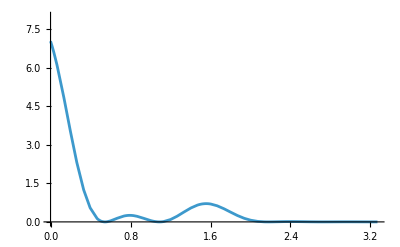

```mathematica
Plot[integrand[W,-Ei[1]/hbar,-8Pi hbar/Ei[1]], {W, 0, (ωmax)hbar},PlotRange ->{Automatic, {0,8}}]
```

```mathematica
(* Plot Pni(ω) *)
P = Labeled[
  ListPlot[data1, 
 ImageSize -> 600,Joined -> True],
  Style["ω",  FontSize -> 20],
  Bottom
]
```

-Graphics-ω

```mathematica
cm = 72/2.54 ;(* centimetre *)
Export[CloudObject["Exports/IP_M1s2sT=E1by4E0e=hbar_v3.png"],P, "png",ImageResolution -> 300]
```

28.3465

CloudObject[https://www.wolframcloud.com/obj/vikrantkumar/Exports/IP_M1s2sT=E1by4E0e=hbar_v3.png]

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[0];
data2 = Table[{ω, Pni[ω,1000]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
Export["Pni_data_M=2_v0.wl", data2, "WL"]; (* Wolfram Language format *)
```

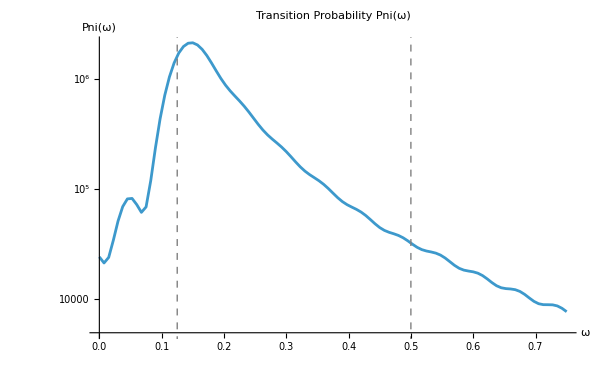

```mathematica
ListLogPlot[data2, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 GridLines -> Automatic,
 ImageSize -> 600,Joined -> True,
Epilog->Table[{Gray, Dashed, Line[{{1/(2*i^2), 0}, {1/(2*i^2), 40000}}]},{i,M}]] (* Control recursion depth *)
```

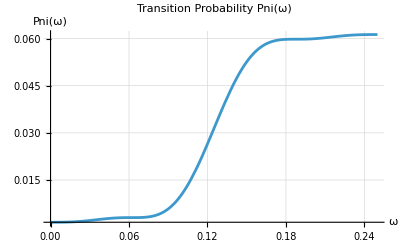

```mathematica
(* Constants and Parameters *)
i = 2;                     (* Defined i *)
Ei =- 1/(2*i^2);             (* Defined E_i *)
Γ23 = Gamma[2/3];          (* Gamma function *)
T[ω_] := 100;             (* T depends on omega *)
E0e = 1;

(* Prefactor term - using En instead of E to avoid conflict *)
prefactor[En_] := 1

(* Sinc-squared term *)
sincTerm[En_, ω_] := Sinc[(En - Ei - ω)/2 * T[ω]]^2

(* Full integrand *)
integrand[En_, ω_] := 1 * prefactor[En] * sincTerm[En, ω]

(* Numerical integration for Pni(ω) *)
Pni[ω_?NumericQ] := NIntegrate[integrand[En, ω], {En, 0, ∞}]

(* Plot range *)
ωmin = 0;
ωmax = -2*Ei;

(* Plot Pni(ω) *)
Plot[Pni[ω], {ω, ωmin, ωmax}, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 PlotRange -> All,
 GridLines -> Automatic,
 PlotPoints -> 30, (* Increase sampling for smoother plot *)
 MaxRecursion -> 3] (* Control recursion depth *)
```